```mathematica
ClearAll["Global'*"]
G[r1_,r2_]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
G2[{r1_,r2_}]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
G3[{r1_,r2_}]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
```

```mathematica
g1[r1_,r2_]={r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))};
g2[r1_,r2_]={r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))};
```

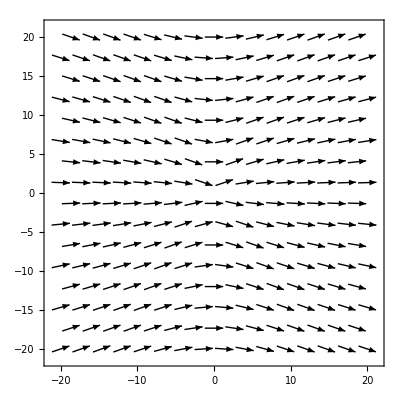

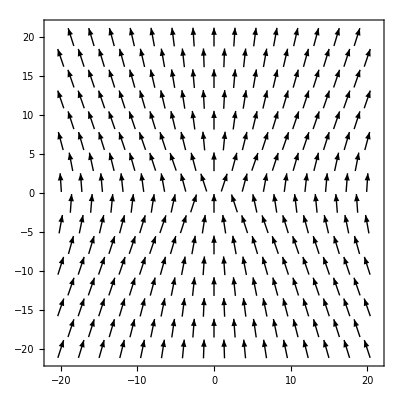

```mathematica
VectorPlot[g1[x,y],{x,-20,20},{y,-20,20}]
VectorPlot[g2[x,y],{x,-20,20},{y,-20,20}]
```

```mathematica
y0:={100,100}
```

```mathematica
y0hat:=y0/Norm[y0];
```

```mathematica
epsilon:=1/Norm[y0]
```

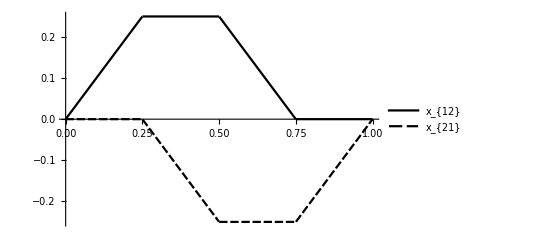

```mathematica
x1[t_]:={2,Piecewise[{{ Mod[t,1],0 ≤ Mod[t,1] ≤ 1/4},{1/4,1/4 ≤ Mod[t,1] ≤ 1/2},{1/4-( Mod[t,1]-1/2),1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}]};
x2[t_]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-( Mod[t,1]-1/4),1/4 ≤ Mod[t,1] ≤ 1/2},{-1/4,1/2≤ Mod[t,1]≤ 3/4},{-1/4 + ( Mod[t,1]-3/4),3/4 ≤ Mod[t,1]≤ 1}}],0};
dx1[t_]:={0,Piecewise[{{1,0 ≤ Mod[t,1] ≤ 1/4},{0,1/4 ≤ Mod[t,1] ≤ 1/2},{-1,1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}]};
dx2[t_]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-1,1/4 ≤ Mod[t,1] ≤ 1/2},{0,1/2≤ Mod[t,1]≤ 3/4},{1,3/4 ≤ Mod[t,1]≤ 1}}],0};
Plot[{x1[t][[2]],x2[t][[1]]},{t,0,1},PlotLegends->LineLegend[{"x_{12}","x_{21}"},LegendFunction->Frame]]
```

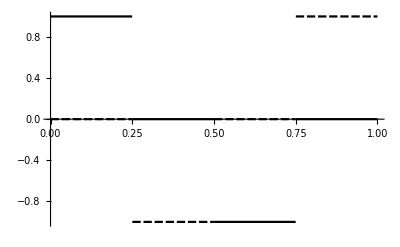

```mathematica
Plot[{dx1[t][[2]],dx2[t][[1]]},{t,0,1}]
```

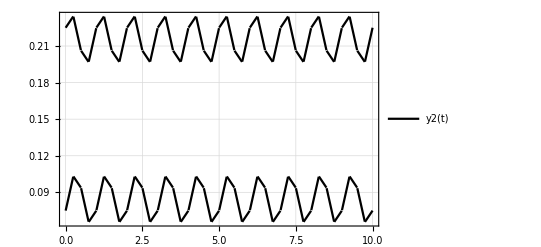

```mathematica
y2[t_]=G2[y0hat].x1[t]+ G2[y0hat].x2[t];
Plot[y2[t],{t,0,10},PlotTheme->"Detailed"]
y22=NDSolveValue[{y'[t]==(3/40)(y0hat.x1[t] dx1[t]+3 y0hat (y0hat.x1[t])(y0hat.dx1[t])+(y0hat.x2[t] )dx2[t]+3 y0hat (y0hat.x2[t])( y0hat.dx2[t]) - y0hat (x1[t].dx1[t])-y0hat (x2[t].dx2[t])-x1[t] (y0hat.dx1[t])-x2[t]( y0hat.dx2[t])),y[0]=={0,0}},y,{t,0,1},Method->"StiffnessSwitching",AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->25];
y23=NDSolveValue[{y'[t]==(3/40)(y2[t] y0hat.dx1[t]+y2[t] y0hat.dx2[t]+y0hat y2[t].(dx1[t]+dx2[t])-(dx1[t]+dx2[t])(y0hat.y2[t])-3(y2[t].y0hat)(y0hat.(dx1[t]+dx2[t])y0hat)),y[0]=={0,0}},y,{t,0,1},Method->"StiffnessSwitching",AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->25];
```

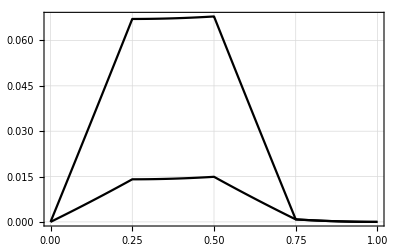

```mathematica
Plot[y22[t],{t,0,1},PlotTheme->"Detailed",PlotLegends->"y_{22}(t)"]
```

```mathematica
x11[t_?NumericQ]:={2,Piecewise[{{ Mod[t,1],0 ≤ Mod[t,1] ≤ 1/4},{1/4,1/4 ≤ Mod[t,1] ≤ 1/2},{1/4-( Mod[t,1]-1/2),1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}]};
x21[t_?NumericQ]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-( Mod[t,1]-1/4),1/4 ≤ Mod[t,1] ≤ 1/2},{-1/4,1/2≤ Mod[t,1]≤ 3/4},{-1/4 + ( Mod[t,1]-3/4),3/4 ≤ Mod[t,1]≤ 1}}],0};
dx11[t_?NumericQ]:={0,Piecewise[{{1,0 ≤ Mod[t,1] ≤ 1/4},{0,1/4 ≤ Mod[t,1] ≤ 1/2},{-1,1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}]};
dx21[t_?NumericQ]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-1,1/4 ≤ Mod[t,1] ≤ 1/2},{0,1/2≤ Mod[t,1]≤ 3/4},{1,3/4 ≤ Mod[t,1]≤ 1}}],0};
y3=NDSolveValue[{b'[t]==G2[b[t]-x11[t]].dx11[t]+G2[b[t]-x21[t]].dx21[t],b[0]==y0},b,{t,0,10},Method->"StiffnessSwitching",AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->25];
```

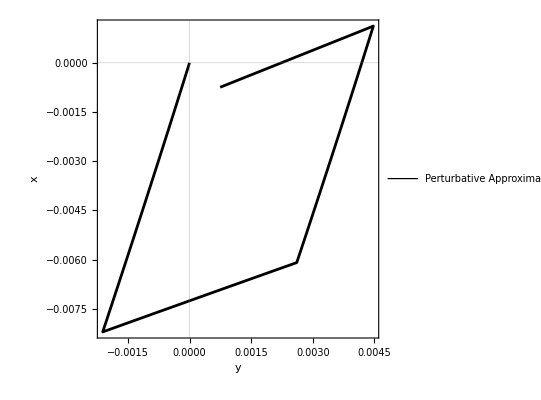

```mathematica
ParametricPlot[{y23[t]},{t,0,1},AspectRatio->1, FrameLabel->{"y","x"},PlotTheme->"Scientific",PerformanceGoal->"Quality",PlotRange->Full,PlotLegends->LineLegend[{"Perturbative Approximation"},LegendFunction->Frame],PlotStyle->{{Black, Thickness[0.005]},{Dashed, Black,Thickness[0.005]}}]
```

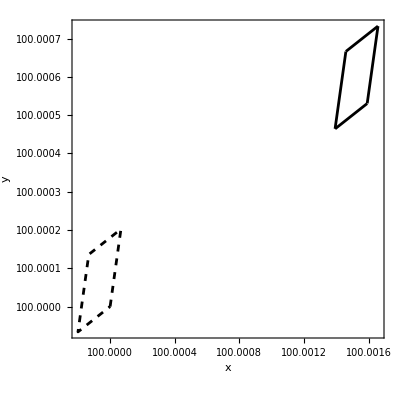

```mathematica
curve=ParametricPlot[{y0+epsilon y2[t]+epsilon^2 y22[t],y3[t]},{t,0,1},AspectRatio->1, FrameLabel->{"x","y"},PlotTheme->"Scientific",PerformanceGoal->"Quality",PlotRange->Full,PlotStyle->{{Black, Thickness[0.005]},{Dashed, Black,Thickness[0.005]}}]
```

```mathematica
dd1 =epsilon^2(y22[1.0]-y22[0])
y2[1]-y2[0]
dd2=y3[1]-y3[0]
dd3=epsilon^3(y23[1]-y23[0])
displ[h_]:=1/(Norm[h]^6)(27/2560)(0.1){h[[2]]^3+h[[2]]h[[1]]^2,-h[[1]]^3-h[[1]]h[[2]]^2}
dd4=N[displ[y0]]
Norm[dd4-dd3]
```

{2.32019×10^-21,7.62349×10^-21}

{0,0}

{2.67874345127×10^-10,-2.7221266737×10^-10}

{2.63671875000002724609375×10^-10,-2.63671875000004482421875×10^-10}

{2.63672×10^-10,-2.63672×10^-10}

5.26668×10^-24

```mathematica
curve2=ParametricPlot[{x1[t],x2[t]},{t,0,1}];
```

```mathematica
Animate[{Show[curve2,Graphics[{PointSize[Large],Point[x1[t]],Point[x2[t]]}]],Show[curve,Graphics[{PointSize[Large],Point[y0+epsilon y2[t]+epsilon^2 y22[t]]}]]},{t,0,1},RefreshRate->30];
y4=ParametricNDSolveValue[{b'[t] == G2[b[t] - x11[t]].dx11[t] + G2[b[t] - x21[t]].dx21[t], b[0] == {b1,b2}}, b[1]-b[0], {t, 0, 1},{b1,b2}, Method -> "StiffnessSwitching",  WorkingPrecision -> 25,PrecisionGoal->25,AccuracyGoal->25];
y4[100,100]
```

{2.69541037932×10^-10,-2.72126097119×10^-10}

```mathematica
y5=ParametricNDSolveValue[{y'[t]==(3/40)epsilon^2(y0hat.x1[t] dx1[t]+3 y0hat (y0hat.x1[t])(y0hat.dx1[t])+(y0hat.x2[t] )dx2[t]+3 y0hat (y0hat.x2[t])( y0hat.dx2[t]) - y0hat (x1[t].dx1[t])-y0hat (x2[t].dx2[t])-x1[t] (y0hat.dx1[t])-x2[t]( y0hat.dx2[t])),y[0]=={b1,b2}},y[1]-y[0],{t,0,1},{b1,b2},Method->"StiffnessSwitching",AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->25];
```

```mathematica
y21[t_,a_,b_]:=G[a,b].(x1[t]+x2[t]);
y6=Integrate[(3/4)(y21[t,q,p] {q,p}.dx1[t]+y21[t,q,p] {q,p}.dx2[t]+{q,p} y21[t,q,p] .(dx1[t]+dx2[t])-(dx1[t]+dx2[t])({q,p}.y21[t,q,p] )-3(y21[t,q,p] .{q,p})({q,p}.(dx1[t]+dx2[t]){q,p})),{t,0,1}]
```

{(27 (p^3+p q^2))/(2560 (p^2+q^2)^(3/2)),-(27 (p^2 q+q^3))/(2560 (p^2+q^2)^(3/2))}

```mathematica
a=0.1;
mu=1;

Ginv[{r1_,r2_},a_]={{(2 (r1^2+2 r2^2))/(3 a √(r1^2+r2^2)),-(2 r1 r2)/(3 a √(r1^2+r2^2))},{-(2 r1 r2)/(3 a √(r1^2+r2^2)),(2 (2 r1^2+r2^2))/(3 a √(r1^2+r2^2))}};
```

```mathematica
K[{r1_,r2_},a_]={{(-81 a^4 (r1^2+r2^2)+18 a^2 (2 r1^2+r2^2)^2)/(4 (9 a^2 (5 r1^4+6 r1^2 r2^2+5 r2^4)-8 (r1^6+4 r1^4 r2^2+4 r1^2 r2^4+r2^6))),(9 a^2 (-2 r1^2 r2^2+9 a^2 (r1^2+r2^2)))/(4 (9 a^2 (5 r1^4+6 r1^2 r2^2+5 r2^4)-8 (r1^6+4 r1^4 r2^2+4 r1^2 r2^4+r2^6)))},{(9 a^2 (-2 r1^2 r2^2+9 a^2 (r1^2+r2^2)))/(4 (9 a^2 (5 r1^4+6 r1^2 r2^2+5 r2^4)-8 (r1^6+4 r1^4 r2^2+4 r1^2 r2^4+r2^6))),(-81 a^4 (r1^2+r2^2)+18 a^2 (r1^2+2 r2^2)^2)/(4 (9 a^2 (5 r1^4+6 r1^2 r2^2+5 r2^4)-8 (r1^6+4 r1^4 r2^2+4 r1^2 r2^4+r2^6)))}};
```

```mathematica
f1[t_]=K[x1[t]-x2[t],a].(Ginv[x1[t]-x2[t],a].dx1[t]-(Ginv[x1[t]-x2[t],a]^2).dx2[t]);
```

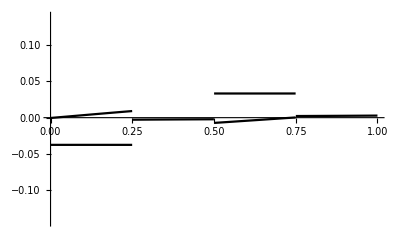

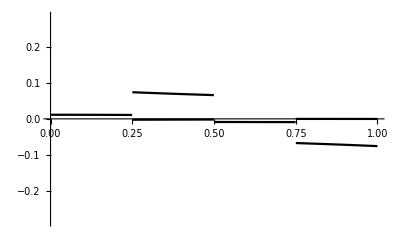

```mathematica
f2[t_]=K[x1[t]-x2[t],a].(Ginv[x1[t]-x2[t],a].dx2[t]-(Ginv[x1[t]-x2[t],a]^2).dx1[t]);

Plot[f1[t],{t,0,1}]
Plot[f2[t],{t,0,1}]
```

```mathematica
Simplify[f1[t]]
Simplify[f2[t]]
```

{Piecewise[{{0., Mod[t,1]>1||Mod[t,1]<0}, {(1. (6552.8-17479.6 Mod[t,1]+20398.3 Mod[t,1]^2-13601.9 Mod[t,1]^3+5668.48 Mod[t,1]^4-1511.8 Mod[t,1]^5+251.989 Mod[t,1]^6-24. Mod[t,1]^7+1. Mod[t,1]^8))/((-3.+Mod[t,1])^2 (724.444-1451.93 Mod[t,1]+1211.96 Mod[t,1]^2-539.325 Mod[t,1]^3+134.944 Mod[t,1]^4-18. Mod[t,1]^5+Mod[t,1]^6)), 3/4<Mod[t,1]≤1}, {-(775.089+3459.2 Mod[t,1]+6777.16 Mod[t,1]^2+7612.98 Mod[t,1]^3+5363.12 Mod[t,1]^4+2426.31 Mod[t,1]^5+688.41 Mod[t,1]^6+112. Mod[t,1]^7+8. Mod[t,1]^8)/(764.375+3422.9 Mod[t,1]+6725.79 Mod[t,1]^2+7574.11 Mod[t,1]^3+5346.55 Mod[t,1]^4+2422.53 Mod[t,1]^5+688.05 Mod[t,1]^6+112. Mod[t,1]^7+8. Mod[t,1]^8), 1/4<Mod[t,1]≤1/2}, {(√(4+Mod[t,1]^2) (-0.054+4.7865 Mod[t,1]+1.17975 Mod[t,1]^2+1.19663 Mod[t,1]^3+0.148313 Mod[t,1]^4+0.075 Mod[t,1]^5))/(252.4+318.02 Mod[t,1]^2+127.505 Mod[t,1]^4+19.9438 Mod[t,1]^6+Mod[t,1]^8), 0≤Mod[t,1]≤1/4}, {(√(45-12 Mod[t,1]+8 Mod[t,1]^2) (-2.91751+5.23372 Mod[t,1]-2.37705 Mod[t,1]^2+0.970106 Mod[t,1]^3-0.17839 Mod[t,1]^4+0.0298311 Mod[t,1]^5))/((5.625-1.5 Mod[t,1]+1. Mod[t,1]^2) (192.345-188.762 Mod[t,1]+175.074 Mod[t,1]^2-69.0188 Mod[t,1]^3+28.6313 Mod[t,1]^4-4.5 Mod[t,1]^5+Mod[t,1]^6)), True}}],Piecewise[{{0., Mod[t,1]>1||Mod[t,1]<0}, {(0.01125 (-3.+Mod[t,1.])^4)/(724.444-1451.93 Mod[t,1.]+1211.96 Mod[t,1.]^2-539.325 Mod[t,1.]^3+134.944 Mod[t,1.]^4-18. Mod[t,1.]^5+Mod[t,1.]^6), 3/4<Mod[t,1]≤1}, {-(2.80371+9.35402 Mod[t,1]+13.0774 Mod[t,1]^2+9.80438 Mod[t,1]^3+4.15688 Mod[t,1]^4+0.945 Mod[t,1]^5+0.09 Mod[t,1]^6)/(764.375+3422.9 Mod[t,1]+6725.79 Mod[t,1]^2+7574.11 Mod[t,1]^3+5346.55 Mod[t,1]^4+2422.53 Mod[t,1]^5+688.05 Mod[t,1]^6+112. Mod[t,1]^7+8. Mod[t,1]^8), 1/4<Mod[t,1]≤1/2}, {(√(4+Mod[t,1]^2) (-4.746+0.0135 Mod[t,1]-5.37975 Mod[t,1]^2-0.296625 Mod[t,1]^3-1.79831 Mod[t,1]^4-0.15 Mod[t,1]^6))/(252.4+318.02 Mod[t,1]^2+127.505 Mod[t,1]^4+19.9438 Mod[t,1]^6+Mod[t,1]^8), 0≤Mod[t,1]≤1/4}, {(√(45-12 Mod[t,1]+8 Mod[t,1]^2) (5.44709-6.2531 Mod[t,1]+6.35391 Mod[t,1]^2-3.01167 Mod[t,1]^3+1.25231 Mod[t,1]^4-0.238649 Mod[t,1]^5+0.053033 Mod[t,1]^6))/((5.625-1.5 Mod[t,1]+1. Mod[t,1]^2) (192.345-188.762 Mod[t,1]+175.074 Mod[t,1]^2-69.0188 Mod[t,1]^3+28.6313 Mod[t,1]^4-4.5 Mod[t,1]^5+Mod[t,1]^6)), True}}]}

{Piecewise[{{0., Mod[t,1]>1||Mod[t,1]<0}, {(2.88+1.26 Mod[t,1]^2+0.18 Mod[t,1]^4+0.01125 Mod[t,1]^6)/(252.4+318.02 Mod[t,1]^2+127.505 Mod[t,1]^4+19.9438 Mod[t,1]^6+Mod[t,1]^8), 0≤Mod[t,1]≤1/4}, {-(56.3836-27.4229 Mod[t,1]+22.7243 Mod[t,1]^2-6.22688 Mod[t,1]^3+2.58188 Mod[t,1]^4-0.405 Mod[t,1]^5+0.09 Mod[t,1]^6)/(8655.52-10802.4 Mod[t,1]+11682.2 Mod[t,1]^2-6716.82 Mod[t,1]^3+3517.22 Mod[t,1]^4-1098.23 Mod[t,1]^5+328.05 Mod[t,1]^6-48. Mod[t,1]^7+8. Mod[t,1]^8), 1/2<Mod[t,1]≤3/4}, {-(0.15 √((-3+Mod[t,1])^2) (728.089-1456.79 Mod[t,1]+1214.39 Mod[t,1]^2-539.865 Mod[t,1]^3+134.989 Mod[t,1]^4-18. Mod[t,1]^5+1. Mod[t,1]^6))/((-3.+Mod[t,1])^2 (724.444-1451.93 Mod[t,1]+1211.96 Mod[t,1]^2-539.325 Mod[t,1]^3+134.944 Mod[t,1]^4-18. Mod[t,1]^5+Mod[t,1]^6)), 3/4<Mod[t,1]≤1}, {(√(25+28 Mod[t,1]+8 Mod[t,1]^2) (1.61231+5.42475 Mod[t,1]+7.63329 Mod[t,1]^2+5.74996 Mod[t,1]^3+2.44555 Mod[t,1]^4+0.556847 Mod[t,1]^5+0.053033 Mod[t,1]^6))/((3.125+3.5 Mod[t,1]+1. Mod[t,1]^2) (30.575+102.672 Mod[t,1]+144.255 Mod[t,1]^2+108.544 Mod[t,1]^3+46.1313 Mod[t,1]^4+10.5 Mod[t,1]^5+Mod[t,1]^6)), True}}],Piecewise[{{0., Mod[t,1]>1||Mod[t,1]<0}, {-(0.0016875 √((-3+Mod[t,1])^2) (-3.+Mod[t,1])^2)/(724.444-1451.93 Mod[t,1]+1211.96 Mod[t,1]^2-539.325 Mod[t,1]^3+134.944 Mod[t,1]^4-18. Mod[t,1]^5+Mod[t,1]^6), 3/4<Mod[t,1]≤1}, {(253.12+318.74 Mod[t,1]^2+127.82 Mod[t,1]^4+19.9888 Mod[t,1]^6+1. Mod[t,1]^8)/(252.4+318.02 Mod[t,1]^2+127.505 Mod[t,1]^4+19.9438 Mod[t,1]^6+Mod[t,1]^8), 0≤Mod[t,1]≤1/4}, {-(8673.46-10822.1 Mod[t,1]+11703.9 Mod[t,1]^2-6729.43 Mod[t,1]^3+3523.45 Mod[t,1]^4-1099.85 Mod[t,1]^5+328.41 Mod[t,1]^6-48. Mod[t,1]^7+8. Mod[t,1]^8)/(8655.52-10802.4 Mod[t,1]+11682.2 Mod[t,1]^2-6716.82 Mod[t,1]^3+3517.22 Mod[t,1]^4-1098.23 Mod[t,1]^5+328.05 Mod[t,1]^6-48. Mod[t,1]^7+8. Mod[t,1]^8), 1/2<Mod[t,1]≤3/4}, {(√(25+28 Mod[t,1]+8 Mod[t,1]^2) (-0.0602642-0.166665 Mod[t,1]-0.185462 Mod[t,1]^2-0.103812 Mod[t,1]^3-0.0292344 Mod[t,1]^4-0.00331456 Mod[t,1]^5))/((3.125+3.5 Mod[t,1]+1. Mod[t,1]^2) (30.575+102.672 Mod[t,1]+144.255 Mod[t,1]^2+108.544 Mod[t,1]^3+46.1313 Mod[t,1]^4+10.5 Mod[t,1]^5+Mod[t,1]^6)), True}}]}

```mathematica
yforces=NDSolveValue[{c'[t]==G2[c[t]-x11[t]].f1[t]+G2[c[t]-x21[t]].f2[t],c[0]==y0},c,{t,0,1},Method->"StiffnessSwitching",  WorkingPrecision -> 25,PrecisionGoal->25,AccuracyGoal->25];
```

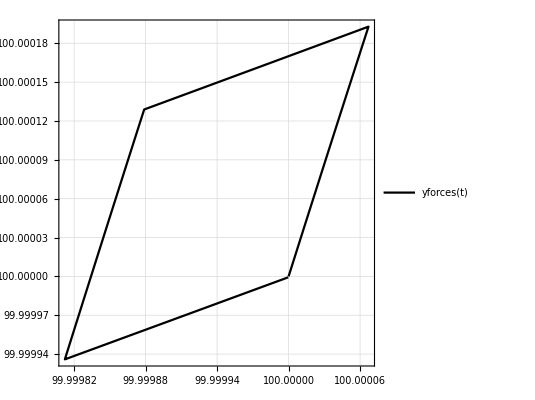

```mathematica
ParametricPlot[{yforces[t]},{t,0,1},PlotTheme->"Detailed"]
```

```mathematica
diffforces = ParametricNDSolveValue[{c'[t] == G2[c[t] - x11[t]].f1[t] + G2[c[t] - x21[t]].f2[t], c[0] == {b1,b2}}, c[1]-c[0],{t, 0, 1}, {b1,b2}, Method -> "StiffnessSwitching"];
diffnoforces= ParametricNDSolveValue[{c'[t] == G2[c[t] - x11[t]].dx11[t] + G2[c[t] - x21[t]].dx21[t], c[0] == {b1,b2}}, c[1]-c[0],{t, 0, 1}, {b1,b2}, Method -> "StiffnessSwitching",WorkingPrecision -> 25,PrecisionGoal->25,AccuracyGoal->25];
```

```mathematica
Simplify[diffforces[y0[[1]],y0[[2]]]].y0
```

-0.00010053

```mathematica
Simplify[diffforces[y0[[1]],y0[[2]]]].({{0,-1},{1,0}}.y0)
```

-0.0000415749

```mathematica
VectorPlot[diffforces[b1,b2],{b1,-10000,10000},{b2,-10000,10000},PlotTheme->"Scientific"]
```

$Aborted

```mathematica
dnftable=Table[{{b1,b2},diffnoforces[b1,b2]},{b1,-10000,10000,20000/15},{b2,-10000,10000,20000/15}];
ListVectorPlot[dnftable,PlotTheme->"Scientific"]
```

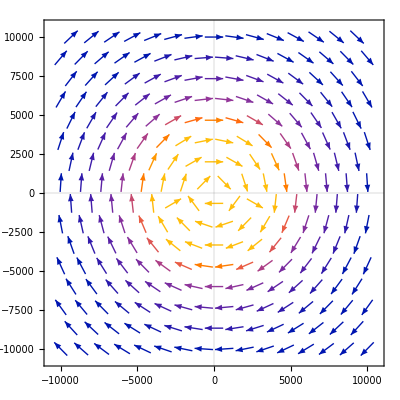

```mathematica
LogLogPlot[{Norm[diffforces[b1,0]],10^(-3)b1^(-1)},{b1,10,100000},PerformanceGoal->"Speed",PlotTheme->"Detailed"]
```

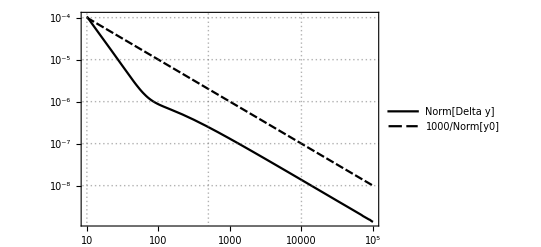

```mathematica
intf=NIntegrate[{f1[t]+f2[t]},{t,0,1}][[1]]//ScientificForm
Simplify[(G2[{p,q}/((p^2+q^2)^(1/2))].intf)/Norm[{p,q}]]//ScientificForm
```

{5.5225×10^-4,-1.47017×10^-3}

({{(3 (2 p^2+q^2))/(40 (p^2+q^2)),(3 p q)/(40 (p^2+q^2))},{(3 p q)/(40 (p^2+q^2)),(3 (p^2+2 q^2))/(40 (p^2+q^2))}}.{5.5225×10^-4,-1.47017×10^-3})/(√(Abs[p]^2+Abs[q]^2))

```mathematica
diffforcesapprox[p_,q_]={(("8.28375"×10^("-5")) p^("2")-("1.10262"×10^("-4")) p q+("4.14187"×10^("-5")) q^("2"))/((p^("2")+q^("2")) √(Abs[p]^("2")+Abs[q]^("2"))),(("-1.10262"×10^("-4")) p^("2")+("4.14187"×10^("-5")) p q-("2.20525"×10^("-4")) q^("2"))/((p^("2")+q^("2")) √(Abs[p]^("2")+Abs[q]^("2")))};
```

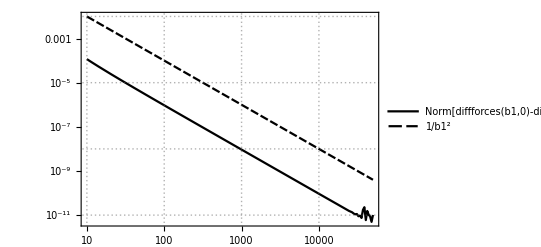

```mathematica
LogLogPlot[{Norm[diffforces[b1,0]-diffforcesapprox[b1,0]],1/(b1^2)},{b1,10,50000},PerformanceGoal->"Speed",PlotTheme->"Detailed"]
```

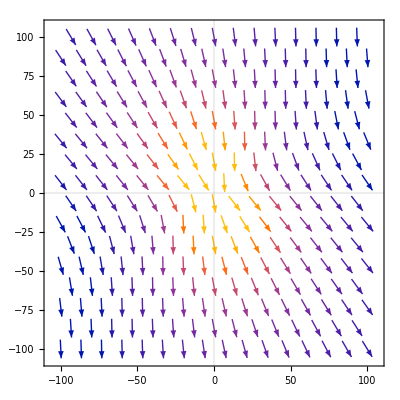

```mathematica
VectorPlot[diffforcesapprox[p,q],{p,-100,100},{q,-100,100},PlotTheme->"Scientific"]
```

```mathematica
ClearAll["Global"]
K2[t_]=Inverse[{{1,0,G2[x1[t]-x2[t]][[1,1]],G2[x1[t]-x2[t]][[1,2]]},
{0,1,G2[x1[t]-x2[t]][[2,1]],G2[x1[t]-x2[t]][[2,2]]},
{G2[x1[t]-x2[t]][[1,1]],G2[x1[t]-x2[t]][[1,2]],1,0},
{G2[x1[t]-x2[t]][[2,1]],G2[x1[t]-x2[t]][[2,2]],0,1}}];
Dimensions[K2[t]]
ff[t_]=K2[t].Join[dx1[t],dx2[t]];
```

{4,4}

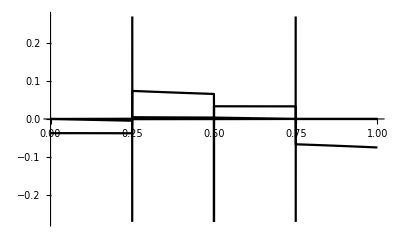

```mathematica
Plot[ff[t],{t,0,1}]
```

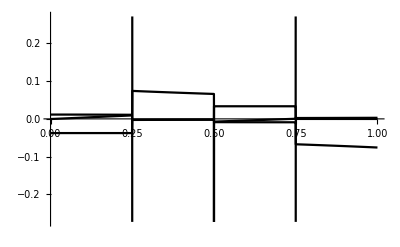

```mathematica
Plot[Join[f1[t],f2[t]],{t,0,1}]
```